# DFT Midterm Project

Jhon Aponte^2, Milagros Delgado^1, Matías Romero^2, Rolando Sánchez^1, and Andrés Toledo^1
[1] School of Physical Sciences and Nanotechnology, Yachay Tech University, Urcuquí - Ecuador
[2] School of Chemical Sciences and Engineering,  Yachay Tech University, Urcuquí - Ecuador

All the code and scripts used in this MidTerm can be found in the repository https://github.com/DaNameless/dft_coursework/midterm

1) Compute ECUT needed to converge the energy < 1 meV/atom . Use energies from 250 to 900 eV (use en_cut . sh), the KPOINTS for this calculation is a mesh 17Χ17Χ17 .

First we are going to set the directory where we are going to work

```mathematica
wrk="/home/rolando/Downloads/Yachay/8th_Semester/dft/dft_coursework/midterm/MidTerm Challenge proyect/al-files/results";
SetDirectory[wrk];
```

Energies from 250 to 900 eV

```mathematica
dataal = Import["ecut.dat"][[All,{1,2}]]//Map[#/{1,1}&,#]&;
dataal//TableForm
```

250 | -3.73811
300 | -3.74326
350 | -3.74591
400 | -3.74663
450 | -3.74695
500 | -3.747
550 | -3.74702
600 | -3.74708
650 | -3.74713
700 | -3.74716
750 | -3.74718
800 | -3.74718
850 | -3.74719
900 | -3.7472

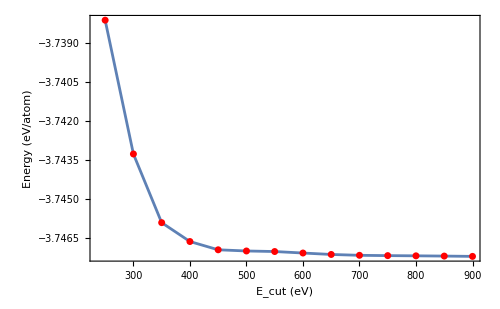

```mathematica
dataal //ListPlot[#,
Frame ->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

Let our convergence criteria to be 1 meV/atom
Using the criteria, let’s obtain a convergence window to find the E_cut

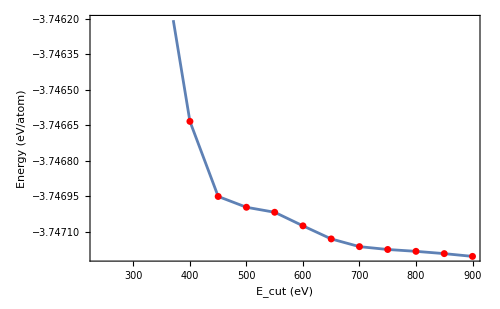

```mathematica
dataal //ListPlot[#,
Frame ->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]],#[[-1,2] ]+10^-3},
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

E_cut = 400

2) Compute KPOINTS needed to converge the energy <1 meV/atom. Use a point mesh from 15 to 28 (use k_points.sh)

Using a mesh from 15 to 28

```mathematica
datakp = Import["kps.dat"][[All, 1;;2]];
datakp//TableForm
```

15 | -3.74157
16 | -3.74576
17 | -3.74664
18 | -3.74583
19 | -3.74372
20 | -3.74461
21 | -3.74588
22 | -3.74632
23 | -3.74528
24 | -3.74442
25 | -3.74498
26 | -3.74592
27 | -3.74584
28 | -3.74528

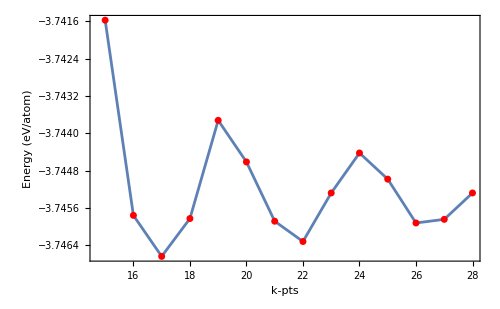

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

Let’ s generate a convergence window of 1 mEv/atomsuch that it encloses the maximum number of k-points

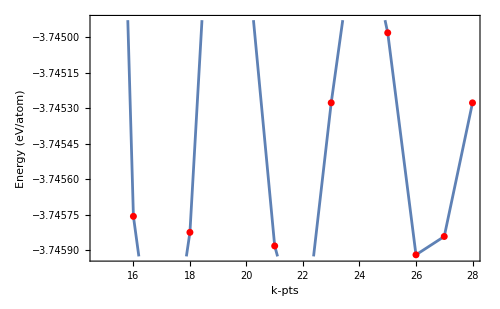

```mathematica
datakp //ListPlot[#,
Frame ->True,
FrameLabel->{"k-pts", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]]-0.65*10^-3,#[[-1,2] ]+0.35 10^-3},
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red, AbsolutePointSize[5], Point[#]}
]&
```

KPOINTS = 25

3) Compute the EOS (use cell.sh from part6_silicon4): for this use the following

initial volumes: Al 16.5

Now, using the script `xcell.sh` we compute the EOS.
The Initial volume is 16.5

```mathematica
val = 16.5;
```

Range for volume of cells

```mathematica
Range[val-3,val+5,0.5]//Map[(#//ToString)<>" "&,#]&//StringJoin
```

13.5 14. 14.5 15. 15.5 16. 16.5 17. 17.5 18. 18.5 19. 19.5 20. 20.5 21. 21.5

```mathematica
cell = Import["cell.dat"]//Map[{#[[1]],#[[2]]}&,#]&;
cell//TableForm
```

13.5 | -3.55636
14. | -3.62266
14.5 | -3.67191
15. | -3.7067
15.5 | -3.7293
16. | -3.74161
16.5 | -3.74519
17. | -3.74142
17.5 | -3.73149
18. | -3.71639
18.5 | -3.69703
19. | -3.67418
19.5 | -3.64844
20. | -3.62016
20.5 | -3.58992
21. | -3.55808
21.5 | -3.52499

Using the Birch-Murnagham equation of state (BM-EO)

```mathematica
eos:=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))
```

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

1.7377+923.257/v^2-55.3327/v^(4/3)-48.9754/v^(2/3)

```mathematica
nlm["BestFitParameters"]
```

{k[1]→1.7377,k[2]→-48.9754,k[3]→-55.3327,k[4]→923.257}

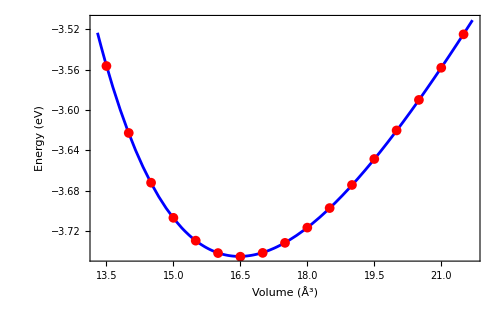

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

4) From EOS determine V_opt, a_0, B_0 and B’

Using the EOS, we can obtain the optimal volume

```mathematica
opvol=FindMinimum[nlm[v],{v,16,17}]
```

{-3.74488,{v→16.4757}}

V_opt = 16.4757

```mathematica
Solve[vol == s^3/4,s]
```

{{s→(-2)^(2/3) vol^(1/3)},{s→2^(2/3) vol^(1/3)},{s→-(-1)^(1/3) 2^(2/3) vol^(1/3)}}

```mathematica
2^(2/3) v^(1/3) /.opvol[[2]]
```

4.03926

a_0 = 4.03926

Bulk modulus

```mathematica
bulkm = v D[nlm[v],{v,2}]/.opvol[[2]]
```

0.479293

```mathematica
UnitConvert[Quantity[bulkm, "Electronvolts"/("Angstroms")^3], "GigaPascals"]
```

76.7912 GPa

B_0 = 76.7912 GPa

Bulk modulus pressure derivative

```mathematica
-v/bulkm D[v D[nlm//Normal,{v,2}],v]/.opvol[[2]]
```

4.76571

B_0' = 4.7657

5) Compute the ground state of the crystal (use Vopt and the script bulk . sh) : from this get the crystallographic data (use FINDSYMM) and the distance between atoms . This info has to be reported in a table similar to Table II of the manual .

Here, we used xbulk . sh script to generate a CONTCAR, with this CONTCAR we obtain a `. cif` file using `>>ase gui CONTCAR -o pos.cif`
Using FINDSYMM, we submit this crystallographic information file to obtain  all the properties in the lattice as show in the table below.

```mathematica
table=Grid[{{Style["Property",Bold],Style["Calculated (PAW-PBE)",Bold],SpanFromLeft},{"Space Group","Fm-3m",SpanFromLeft},{"a = b = c (Å)","4.03924",SpanFromLeft},{"alpha = beta = gamma (°)","90.0000",SpanFromLeft},{"Volumen (Å^3)","65.90247",SpanFromLeft},{"B0 (GPa)","76.7912",SpanFromLeft},{"B'0","4.76571",SpanFromLeft},{"sites","u","v","w"},{"Al(1)","0.00","0.00","0.00"}},Frame->All,Alignment->{{Left,Center,Center,Center},Automatic},Background->{None,{LightGray,None}},Spacings->{2,1.2}]
```

Property | Calculated (PAW-PBE) |  | 
Space Group | Fm-3m |  | 
a = b = c (Å) | 4.03924 |  | 
alpha = beta = gamma (°) | 90.0000 |  | 
Volumen (Å^3) | 65.90247 |  | 
B0 (GPa) | 76.7912 |  | 
B'0 | 4.76571 |  | 
sites | u | v | w
Al(1) | 0.00 | 0.00 | 0.00

6) Show the plot of the PDOS (what is the composition in terms of s, p and d states?) and 

the charge density (use VESTA and display using boundary menu with 3x3x3), Is the

system metal, semiconductor or insulator? Explain.

```mathematica
input=Import["DOSCAR-bulk", "Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

8.04548

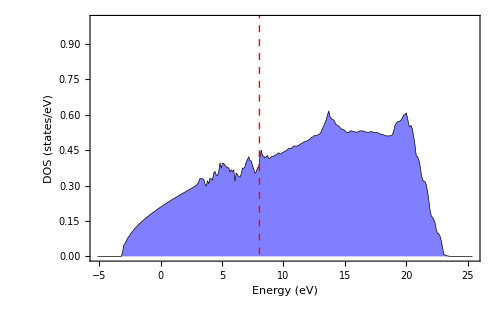

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{All, {0,1}}]
```

The DOS plot for aluminum shows the relationship between available electronic states (in units of states/eV) and energy (in eV) . In the case of aluminum, the density of states is significant at the Fermi level (around 0 eV), indicating a large number of accessible electronic states for electrons . The absence of a band gap confirms that aluminum' s orbitals overlap continuously, allowing electrons to move freely. This is a typical feature of metals, where electrons in the conduction band require no additional energy to move, explaining aluminum' s high electrical and thermal conductivity .

### Partial density of States (PDOs)

the arrange of the data PDOS is according to the AO :
 energy,  s,  p_y p_z p_x d_ {xy} d_ {yz} d_ {z2 - r2} d_ {xz} d_ {x2 - y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
```

```mathematica
dosall=(dos1)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
f[py]=Map[{#[[1]],#[[3]]}&,#]&;
f[pz]=Map[{#[[1]],#[[4]]}&,#]&;
f[px]=Map[{#[[1]],#[[5]]}&,#]&;
```

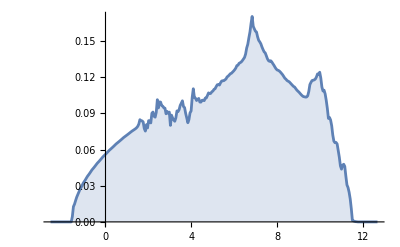

```mathematica
dosall//f[total]//ListPlot[#,Joined->True,Filling->Axis]&
```

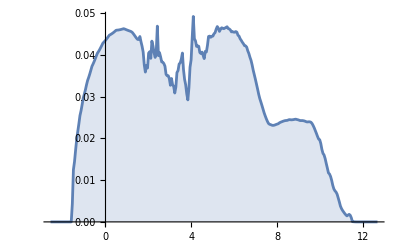

```mathematica
dosall//f[s]//ListPlot[#,Joined->True,Filling->Axis]&
```

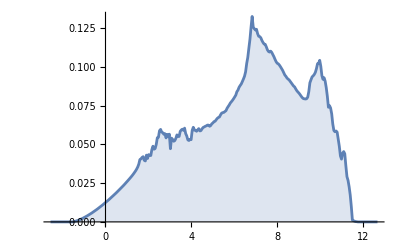

```mathematica
dosall//f[p]//ListPlot[#,Joined->True,Filling->Axis]&
```

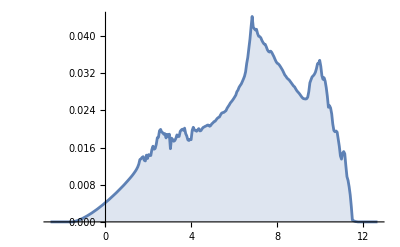

```mathematica
dosall//f[py]//ListPlot[#,Joined->True,Filling->Axis]&
```

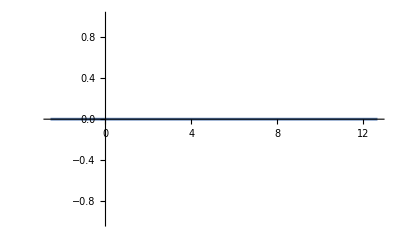

```mathematica
dosall//f[d]//ListPlot[#,Joined->True,Filling->Axis]&
```

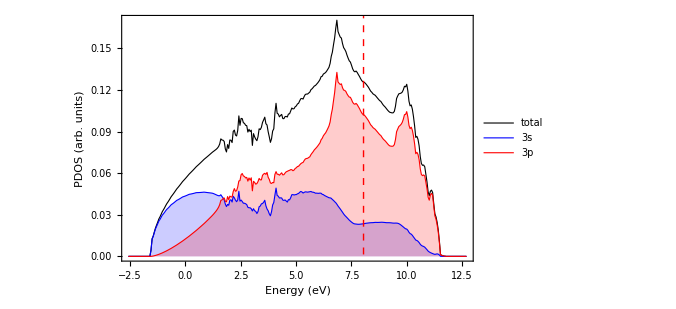

```mathematica
{dosall//f[total],dosall//f[s], dosall//f[p] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
PlotRange->All,
PlotLegends->Placed[{"total", "3s", "3p"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

The graph shows that both 3 s and 3 p orbitals contribute to aluminum' s density of states (DOS) . The 3 s orbital appears as a narrow peak around - 2 eV, indicating localized, low - dispersion states . The broader 3 p band, spanning from - 2.5 eV to above the Fermi level, reflects greater orbital overlap and delocalization . At the Fermi level, the DOS is continuous, mainly due to 3 p states, which is key to aluminum' s metallic conductivity . The combined presence of 3 s and 3 p orbitals near the Fermi level facilitates electron mobility and efficient conduction .

8) Compute the band structure of the ground state of the crystal along the following high-symmetry points path: Γ—X—U—W—K—Γ—L, use 45 intersections in the KPOINTS-bs.

Using `xbs .sh` script, we obtain the PROCAR_file that contains information about the band structure computed along the path Γ—X—U—W—K—Γ—L.

```mathematica
Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];
```

```mathematica
ef=input[[6,4]];
```

```mathematica
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{270,6}

```mathematica
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{Γ,X,U,W,K,Γ,L}

```mathematica
bands=Import["bandData","Table"][[2;;Nbands Nkpt+1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
kp=Import["kpts","Table"][[2;;Nkpt+1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

```mathematica
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}]
```

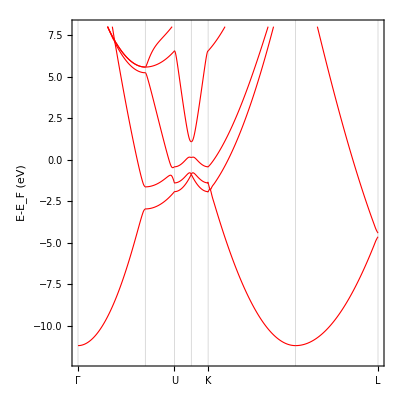

```mathematica
ListPlot[Table[bd[i],{i,1,Nbands}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,8}}]
```

Aluminum (Al) in the fm-3m (face - centered cubic, FCC) structure is a metal . This is because its band structure typically shows bands crossing the Fermi level, indicating no band gap and the presence of conducting electrons . The graphic likely confirms this with bands intersecting the Fermi level (0 eV) along the high - symmetry path of it' s structure .

9) Compute the band structure of the ground state of the crystal along the following high-

symmetry points path: Γ—X—U—W—K—Γ—L, use 45 intersections in the KPOINTS-bs

.

Using the script `xatom . sh` we obtain the isolated energy for the atom.

```mathematica
bulkdata = Import["bulk.dat"];
atomdata = Import["../results_atom/atom.dat"];
Ebulk = bulkdata[[1]][[2]];
Eatom = atomdata[[1]][[2]];
```

```mathematica
Subscript[E, cohesion]=Ebulk-Eatom
```

-3.47073

The calculation of the cohesion energy is correctly performed by comparing the energy of the bulk system (ebulk) with that of an isolated atom (eatom), yielding a result of − 3.47073 eV . This negative value is physically meaningful, as it indicates that the bulk configuration is more stable than the isolated atom, which is typical for cohesive bonding in solids.